```mathematica
Clear["Global`*"]
ClearSystemCache[];
```

```mathematica
h[kx_,ky_,α_,β_,δ_]:= Module[{σ0,σ1,σ2,σ3,Γ13,Γ30,Γ03,Γ12,Γ31,Γ21,Γ32, hh},
(* Pauli Matrices *)
σ0 = {{1,0},{0,1}};
σ1 = {{0,1},{1,0}};
σ2 = {{0,-ⅈ},{ⅈ ,0}};
σ3 = {{1,0},{0,-1}};

(* Gamma Matrices *)
Γ13 = KroneckerProduct[σ1,σ3];
Γ30 = KroneckerProduct[σ3,σ0];
Γ03 = KroneckerProduct[σ0,σ3];
Γ12 = KroneckerProduct[σ1,σ2];
Γ31 = KroneckerProduct[σ3,σ1];
Γ21 = KroneckerProduct[σ2,σ1];
Γ32 = KroneckerProduct[σ3,σ2];

(* Hamiltonian *)
hh= N[Γ13/2 + (α/2)*(Cos[kx] + Cos[ky])*(Γ30 + Γ03) + (Γ12 + Γ31)*Sin[kx] + (Γ21 + Γ32)*Sin[ky] - Γ03 + (β/2)*Cos[kx]*(Cos[ky] - δ)*(Γ03 - Γ30)]
]
σ0 = {{1,0},{0,1}};
σ3 = {{1,0},{0,-1}};
Γ03 = KroneckerProduct[σ0,σ3]
```

{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}}

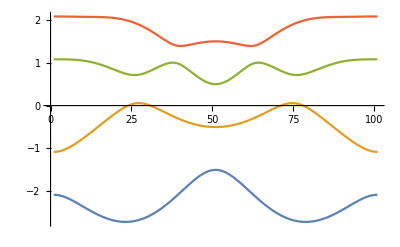

```mathematica
ListPlot[Transpose[Table[Sort[Eigenvalues[h[Pi,kx,-1.5,0,0]]],{kx,-Pi,Pi,2*Pi/100}]],Joined -> True,PlotRange->All]
```

```mathematica
MatrixForm[h[kx,ky,α,β,δ]]
```

(-1.+α (Cos[kx]+Cos[ky]) | Sin[kx]-(0.+1. ⅈ) Sin[ky] | 0.5 | (0.-1. ⅈ) Sin[kx]-(0.+1. ⅈ) Sin[ky]
Sin[kx]+(0.+1. ⅈ) Sin[ky] | 1.-1. β Cos[kx] (-1. δ+Cos[ky]) | (0.+1. ⅈ) Sin[kx]-(0.+1. ⅈ) Sin[ky] | -0.5
0.5 | (0.-1. ⅈ) Sin[kx]+(0.+1. ⅈ) Sin[ky] | -1.+β Cos[kx] (-1. δ+Cos[ky]) | -1. Sin[kx]+(0.+1. ⅈ) Sin[ky]
(0.+1. ⅈ) Sin[kx]+(0.+1. ⅈ) Sin[ky] | -0.5 | -1. Sin[kx]-(0.+1. ⅈ) Sin[ky] | 1.-1. α (Cos[kx]+Cos[ky]))

```mathematica
MatrixForm[Γ03.h[kx,ky,α,β,δ].Inverse[Γ03]]
```

(-1.+α (Cos[kx]+Cos[ky]) | 0.-Sin[kx]+(0.+1. ⅈ) Sin[ky] | 0.5 | 0.+(0.+1. ⅈ) Sin[kx]+(0.+1. ⅈ) Sin[ky]
0.-Sin[kx]-(0.+1. ⅈ) Sin[ky] | 1.-1. β Cos[kx] (-1. δ+Cos[ky]) | 0.-(0.+1. ⅈ) Sin[kx]+(0.+1. ⅈ) Sin[ky] | -0.5
0.5 | 0.+(0.+1. ⅈ) Sin[kx]-(0.+1. ⅈ) Sin[ky] | -1.+β Cos[kx] (-1. δ+Cos[ky]) | 0.+1. Sin[kx]-(0.+1. ⅈ) Sin[ky]
0.-(0.+1. ⅈ) Sin[kx]-(0.+1. ⅈ) Sin[ky] | -0.5 | 0.+1. Sin[kx]+(0.+1. ⅈ) Sin[ky] | 1.-1. α (Cos[kx]+Cos[ky]))

```mathematica
(* Question 3b: for zero values, the eigenvale is +1 *)
{eigs,vecs}=Eigensystem[h[0,0,-1.5,1.5,-1]];
list1=Partition[Riffle[eigs,vecs],2];
list2=Sort[list1,#1[[1]]<#2[[1]]&];
list2[[1,2]]-Γ03.list2[[1,2]]
list2[[2,2]]-Γ03.list2[[2,2]]

{eigs,vecs}=Eigensystem[h[Pi,0,-1.5,1.5,-1]];
list1=Partition[Riffle[eigs,vecs],2];
list2=Sort[list1,#1[[1]]<#2[[1]]&];
list2[[1,2]]-Γ03.list2[[1,2]]
list2[[2,2]]-Γ03.list2[[2,2]]

{eigs,vecs}=Eigensystem[h[0,Pi,-1.5,1.5,-1]];
list1=Partition[Riffle[eigs,vecs],2];
list2=Sort[list1,#1[[1]]<#2[[1]]&];
list2[[1,2]]-Γ03.list2[[1,2]]
list2[[2,2]]-Γ03.list2[[2,2]]

{eigs,vecs}=Eigensystem[h[Pi,Pi,-1.5,1.5,-1]];
list1=Partition[Riffle[eigs,vecs],2];
list2=Sort[list1,#1[[1]]<#2[[1]]&];
list2[[1,2]]-Γ03.list2[[1,2]]
list2[[2,2]]-Γ03.list2[[2,2]]
```

{0.,0.,0.,0.}

{0.,1.99319,0.,0.164961}

{0.,0.,0.,0.}

{0.,0.,0.,0.}

{0.,0.,0.,0.}

«1 more identical outputs»

{0.,0.320364,0.,1.97417}

{0.,0.,0.,0.}

```mathematica
(* Wilson Loop around kx for several values of ky*)
α1 = -1.5; β1 = 0; γ1 = 0; NN = 1000;
α2 = -1.5; β2 = 1.5; γ2 = 1;
kkx = Subdivide[0,2*Pi, NN]; kky = Subdivide[-Pi,Pi, 250];
wlp1 =ConstantArray[1,Length[kky]]; wlp2 = ConstantArray[1,Length[kky]];
For[q=1, q<=Length[kky],q++,
	For[qq=2,qq<=NN,qq++,
	{eigs,vecs}=Eigensystem[h[kkx[[qq]],kky[[q]],α1,β1,γ1]];
	list1=Partition[Riffle[eigs,vecs],2];
	list2=Sort[list1,#1[[1]]<#2[[1]]&];

	{eigs1,vecs1}=Eigensystem[h[kkx[[qq-1]],kky[[q]],α1,β1,γ1]];
	list11=Partition[Riffle[eigs1,vecs1],2];
	list22=Sort[list11,#1[[1]]<#2[[1]]&];

	wlp1[[q]] = wlp1[[q]]*list2[[1,2]].list22[[1,2]] ;
	wlp2[[q]]= wlp2[[q]]*list2[[2,2]].list22[[2,2]]
]
]
```

General::munfl: (1.67923×10^-307-3.97905×10^-308 ⅈ) (-0.660547-0.0303678 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.2065×10^-307-3.1499×10^-307 ⅈ) (-0.596396-0.253504 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-6.72244×10^-308+6.28069×10^-308 ⅈ) (-0.602818-0.241627 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1001

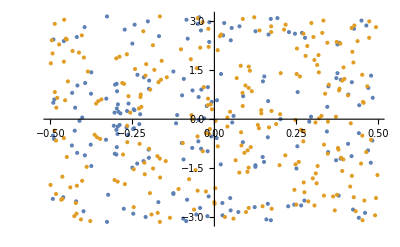

```mathematica
mylist1=Transpose@{Re[Log[wlp1]/(ⅈ*2*Pi)],kky};
mylist2=Transpose@{Re[Log[wlp2]/(ⅈ*2*Pi)],kky};
ListPlot[{mylist1,mylist2}]
```

```mathematica
α1 = -1.5; β1 = 0; γ1 = 0; NN = 1000;
α2 = -1.5; β2 = 1.5; γ2 = 1;
kkx = Subdivide[0,N[2*Pi], NN];
wlp1 =ConstantArray[1,Length[kky]]; wlp2 = ConstantArray[1,Length[kky]];
For[qq=2,qq<=NN,qq++,
	{eigs,vecs}=Eigensystem[h[kkx[[qq]],N[Pi/2],α2,β2,γ2]];
	list1=Partition[Riffle[eigs,vecs],2];
	list2=Sort[list1,#1[[1]]<#2[[1]]&];

	{eigs1,vecs1}=Eigensystem[h[kkx[[qq-1]],N[Pi/2],α2,β2,γ2]];
	list11=Partition[Riffle[eigs1,vecs1],2];
	list22=Sort[list11,#1[[1]]<#2[[1]]&];

	wlp1[[qq]] = list2[[1,2]].list22[[1,2]] ;
	wlp2[[qq]]= list2[[2,2]].list22[[2,2]]
]
```

Set::partw: Part 252 of {1,0.78086+0.00278812 ⅈ,-0.780811-0.00834562 ⅈ,-0.780714-0.0138655 ⅈ,-0.780568-0.0193473 ⅈ,-0.780376-0.0247907 ⅈ,-0.780138-0.0301954 ⅈ,-0.779855-0.035561 ⅈ,-0.779527-0.0408873 ⅈ,-0.779155-0.0461739 ⅈ,«241»} does not exist.

Set::partw: Part 252 of {1,0.728925-0.68459 ⅈ,0.439366+0.898303 ⅈ,0.440162+0.897908 ⅈ,0.440975+0.8975 ⅈ,0.441805+0.897081 ⅈ,0.442653+0.896649 ⅈ,0.443517+0.896205 ⅈ,0.444398+0.895749 ⅈ,0.445296+0.895281 ⅈ,«241»} does not exist.

Set::partw: Part 253 of {1,0.78086+0.00278812 ⅈ,-0.780811-0.00834562 ⅈ,-0.780714-0.0138655 ⅈ,-0.780568-0.0193473 ⅈ,-0.780376-0.0247907 ⅈ,-0.780138-0.0301954 ⅈ,-0.779855-0.035561 ⅈ,-0.779527-0.0408873 ⅈ,-0.779155-0.0461739 ⅈ,«241»} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

```mathematica
list1
o=Flatten[Orthogonalize/@FindClusters[N@eigs->vecs],1]
```

{{-3.70155,{0.00210643+0.666376 ⅈ,0.234686-5.56618×10^-6 ⅈ,-0.00210183-0.668105 ⅈ,0.233435+0. ⅈ}},{3.,{0.000882913+0.00221583 ⅈ,-0.711531-0.0000617985 ⅈ,0.000894272-0.00222692 ⅈ,0.702646+0. ⅈ}},{2.70154,{-0.000716793-0.233157 ⅈ,0.662302+0.000068003 ⅈ,0.000729872+0.23494 ⅈ,0.672157+0. ⅈ}},{-1.99998,{-0.600412-0.3756 ⅈ,-0.000458333-0.000940145 ⅈ,-0.598522-0.374432 ⅈ,0.00104976+0. ⅈ}}}

{{0.00210643+0.666376 ⅈ,0.234686-5.56618×10^-6 ⅈ,-0.00210183-0.668105 ⅈ,0.233435+0. ⅈ},{-0.600412-0.3756 ⅈ,-0.000458333-0.000940145 ⅈ,-0.598522-0.374432 ⅈ,0.00104976+2.19493×10^-17 ⅈ},{0.000882913+0.00221583 ⅈ,-0.711531-0.0000617985 ⅈ,0.000894272-0.00222692 ⅈ,0.702646+0. ⅈ},{-0.000716793-0.233157 ⅈ,0.662302+0.000068003 ⅈ,0.000729872+0.23494 ⅈ,0.672157+5.09461×10^-19 ⅈ}}

```mathematica
o[[1]].Transpose[o[[2]]]
```

0.000261506-0.00044964 ⅈ

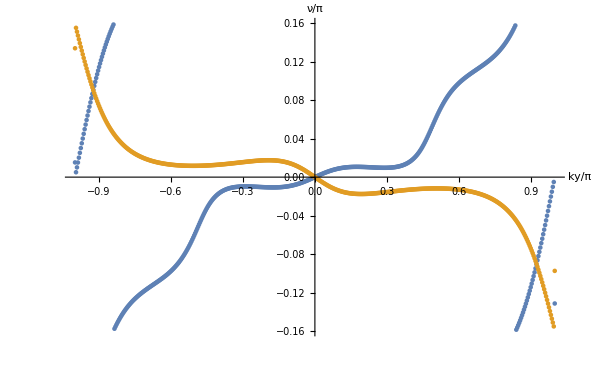

```mathematica
data  = Import["/home/r_floren/Documents/MATLAB/Wannier0.txt","Table"];
data1 = Import["/home/r_floren/Documents/MATLAB/Wannier02.txt","Table"];
ListPlot[{data1/Pi,data/Pi},AxesLabel->{ky/π,ν/π}]
```

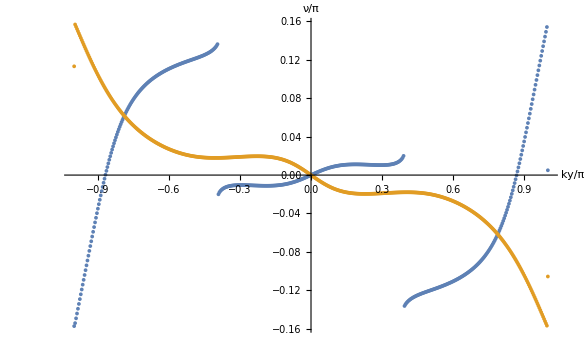

```mathematica
data2  = Import["/home/r_floren/Documents/MATLAB/Wannier1.txt","Table"];
data12 = Import["/home/r_floren/Documents/MATLAB/Wannier12.txt","Table"];
ListPlot[{data12/Pi,data2/Pi},AxesLabel->{ky/π,ν/π}]
```

## Assignment 3

```mathematica
h2[kx_,ky_,t_,t1_,λ_]:= Module[{α1,α2,α3,k},
(* Vectors *)
α1={N[2*λ],0};
α2={λ,N[Sqrt[3]]*λ};
α3={λ,-N[Sqrt[3]]*λ};
k={kx,ky};

(* Hamiltonian *)
N[{{0,t,0,t1*Exp[-ⅈ*k.α3],0,t},{t,0,t,0,t1*Exp[ⅈ*k.α2],0},{0,t,0,t,0,t1*Exp[ⅈ*k.α1]},{t1*Exp[ⅈ*k.α3],0,t,0,t,0},{0,t1*Exp[-ⅈ*k.α2],0,t,0,t},{t,0,t1*Exp[-ⅈ*k.α1],0,t,0}}]

]
```

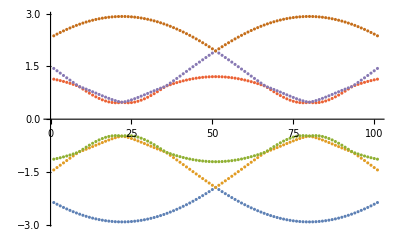

```mathematica
ListPlot[Transpose[Table[Sort[Eigenvalues[h2[2*Pi/Sqrt[3],kx,1,1,1]]],{kx,-Pi,Pi,Pi/50}]]]
```

```mathematica
Plot3D[Sort[Eigenvalues[h2[kx,ky,1,1.5,1]]],{kx,-Pi,Pi},{ky,-Pi,Pi}]
```

-Graphics3D-

```mathematica
h2[2*Pi/3,0,1,0.5,1]//MatrixForm
```

(0. | 1. | 0. | -0.25-0.433013 ⅈ | 0. | 1.
1. | 0. | 1. | 0. | -0.25+0.433013 ⅈ | 0.
0. | 1. | 0. | 1. | 0. | -0.25-0.433013 ⅈ
-0.25+0.433013 ⅈ | 0. | 1. | 0. | 1. | 0.
0. | -0.25-0.433013 ⅈ | 0. | 1. | 0. | 1.
1. | 0. | -0.25+0.433013 ⅈ | 0. | 1. | 0.)

```mathematica
Plot3D[Sort[Eigenvalues[h2[kx,ky,1,1,1]]],{kx,-Pi,Pi},{ky,-Pi,Pi}]
```

-Graphics3D-

```mathematica
(*C_2 Symmetries*)
R2=ConstantArray[0,{6,6}];
R2[[1,4]]=1; R2[[2,5]]=1; R2[[3,6]]=1; R2[[4,1]]=1; R2[[5,2]]=1; R2[[6,3]]=1;

{eigs1,vecs1}=Eigensystem[h2[0,0,1,1.5,1]];
list1=Partition[Riffle[eigs1,vecs1],2];
list2=Sort[list1,#1[[1]]<#2[[1]]&];
hd1=ConstantArray[0,{2,2}];
For[i=2,i<=3,i++,
For [ii=2,ii<=3,ii++,hd1[[i-1,ii-1]]=list2[[i,2]].R2.(list2[[ii,2]])];];
{eigs11,vecs11}=Eigensystem[hd1]

{eigs2,vecs2}=Eigensystem[h2[Pi/2,Pi/(2*Sqrt[3]),1,1.5,1]];
list21=Partition[Riffle[eigs2,vecs2],2];
list22=Sort[list21,#1[[1]]<#2[[1]]&];
hd2=ConstantArray[0,{2,2}];
For[i=2,i<=3,i++,
For [ii=2,ii<=3,ii++,hd2[[i-1,ii-1]]=list22[[i,2]].R2.(list22[[ii,2]])];];
{eigs22,vecs22}=Eigensystem[hd2]
```

{{-1.,-1.},{{-0.998068+0. ⅈ,-0.0621374+0. ⅈ},{0.0621374+0. ⅈ,-0.998068+0. ⅈ}}}

{{-1.,1.},{{1.-1.0634×10^-15 ⅈ,1.02002×10^-15+0. ⅈ},{1.02002×10^-15-1.08468×10^-30 ⅈ,-1.+0. ⅈ}}}

```mathematica
list22[[1,2]].(R3+Inverse[R3]).list22[[1,2]]
list22//MatrixForm
R3+Inverse[R3]//MatrixForm
h2[2*Pi/3,0,1,0.5,1]//MatrixForm
```

1.88462-0.466321 ⅈ

(-1.80278 | {0.396297-0.0980581 ⅈ,-0.408248-1.35974×10^-16 ⅈ,0.396297-0.0980581 ⅈ,-0.408248-1.35974×10^-16 ⅈ,0.396297-0.0980581 ⅈ,-0.408248+0. ⅈ}
-1.32288 | {-0.272772-0.0944911 ⅈ,-0.288675-9.61481×10^-17 ⅈ,0.545545+0.188982 ⅈ,-0.288675-9.61481×10^-17 ⅈ,-0.272772-0.0944911 ⅈ,0.57735+0. ⅈ}
-1.32288 | {-0.498967-0.0321307 ⅈ,0.481996-0.132964 ⅈ,1.47115×10^-17+3.6004×10^-17 ⅈ,-0.481996+0.132964 ⅈ,0.498967+0.0321307 ⅈ,0.+0. ⅈ}
1.32288 | {-0.498967-0.0321307 ⅈ,-0.481996+0.132964 ⅈ,1.3708×10^-17+1.16312×10^-17 ⅈ,0.481996-0.132964 ⅈ,0.498967+0.0321307 ⅈ,0.+0. ⅈ}
1.32288 | {0.272772+0.0944911 ⅈ,-0.288675-9.61481×10^-17 ⅈ,-0.545545-0.188982 ⅈ,-0.288675-9.61481×10^-17 ⅈ,0.272772+0.0944911 ⅈ,0.57735+0. ⅈ}
1.80278 | {-0.396297+0.0980581 ⅈ,-0.408248-1.35974×10^-16 ⅈ,-0.396297+0.0980581 ⅈ,-0.408248-1.35974×10^-16 ⅈ,-0.396297+0.0980581 ⅈ,-0.408248+0. ⅈ})

(0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0)

(0. | 1. | 0. | -0.25-0.433013 ⅈ | 0. | 1.
1. | 0. | 1. | 0. | -0.25+0.433013 ⅈ | 0.
0. | 1. | 0. | 1. | 0. | -0.25-0.433013 ⅈ
-0.25+0.433013 ⅈ | 0. | 1. | 0. | 1. | 0.
0. | -0.25-0.433013 ⅈ | 0. | 1. | 0. | 1.
1. | 0. | -0.25+0.433013 ⅈ | 0. | 1. | 0.)

```mathematica
(*C_3 Symmetries*)
R3=ConstantArray[0,{6,6}];
R3[[1,3]]=1; R3[[2,4]]=1; R3[[3,5]]=1; R3[[4,6]]=1; R3[[5,1]]=1; R3[[6,2]]=1;

{eigs1,vecs1}=Eigensystem[h2[0,0,1,0.5,1]];
list1=Partition[Riffle[eigs1,vecs1],2];
list2=Sort[list1,#1[[1]]<#2[[1]]&];
hd1=ConstantArray[0,{2,2}];
For[i=2,i<=3,i++,
For [ii=2,ii<=3,ii++,hd1[[i-1,ii-1]]=list2[[i,2]].(R3+Transpose[R3]).(list2[[ii,2]])];];
{eigs11,vecs11}=Eigensystem[hd1]

{eigs2,vecs2}=Eigensystem[h2[2*Pi/3,0,1,0.5,1]];
list21=Partition[Riffle[eigs2,vecs2],2];
list22=Sort[list21,#1[[1]]<#2[[1]]&];
hd2=ConstantArray[0,{2,2}];
For[i=2,i<=3,i++,
For [ii=2,ii<=3,ii++,hd2[[i-1,ii-1]]=list22[[i,2]].(R3+Transpose[R3]).(list22[[ii,2]])];];
{eigs22,vecs22}=Eigensystem[hd2]
```

{{-1.,-1.},{{0.122183+0. ⅈ,0.992508+0. ⅈ},{-0.992508+0. ⅈ,0.122183+0. ⅈ}}}

{{-0.892857-0.309295 ⅈ,-0.925152+0.192225 ⅈ},{{1.+0. ⅈ,0.+0. ⅈ},{-9.01874×10^-17-3.2625×10^-16 ⅈ,1.+0. ⅈ}}}

```mathematica
Inverse[R3].h2[2*Pi/3,0,1,0.5,1].R3//MatrixForm
h2[2*Pi/3,0,1,0.5,1]//MatrixForm
```

(0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ | -0.25-0.433013 ⅈ | 0.+0. ⅈ | 1.+0. ⅈ
1.+0. ⅈ | 0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ | -0.25+0.433013 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ | -0.25-0.433013 ⅈ
-0.25+0.433013 ⅈ | 0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -0.25-0.433013 ⅈ | 0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ | 1.+0. ⅈ
1.+0. ⅈ | 0.+0. ⅈ | -0.25+0.433013 ⅈ | 0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ)

(0. | 1. | 0. | -0.25-0.433013 ⅈ | 0. | 1.
1. | 0. | 1. | 0. | -0.25+0.433013 ⅈ | 0.
0. | 1. | 0. | 1. | 0. | -0.25-0.433013 ⅈ
-0.25+0.433013 ⅈ | 0. | 1. | 0. | 1. | 0.
0. | -0.25-0.433013 ⅈ | 0. | 1. | 0. | 1.
1. | 0. | -0.25+0.433013 ⅈ | 0. | 1. | 0.)

```mathematica
HGK[t1_,t2_]:=Module[{th1,th2,th3,t0,T0,Th1,Th2,Th3,h0,hh},
t0=ConstantArray[0,{9,9}];
T0=ConstantArray[0,{6,6}];
For[i=1,i<=6-1,i++,T0[[i,i+1]]=N[t1];];
T0[[6,1]]=N[t1];
For[i=1,i<=9,i++,t0[[i,i]]=1;];
th1={{0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0}};
th2={{0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}};
th3={{0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}};
Th1=ConstantArray[0,{6,6}]; Th2=ConstantArray[0,{6,6}]; Th3=ConstantArray[0,{6,6}];
Th1[[5,2]]=N[t2]; Th2[[4,1]]=N[t2];Th3[[3,6]]=N[t2];
hh=KroneckerProduct[th1,Th1]+ConjugateTranspose[KroneckerProduct[th1,Th1]]+KroneckerProduct[th2,Th2]+ConjugateTranspose[KroneckerProduct[th2,Th2]]+KroneckerProduct[th3,Th3]+ConjugateTranspose[KroneckerProduct[th3,Th3]];
h0=KroneckerProduct[t0,T0]+ConjugateTranspose[KroneckerProduct[t0,T0]];
h0+hh 
]
```

```mathematica
t1=1;
```

```mathematica
ListPlot[Transpose[Table[Sort[Eigenvalues[HGK[1,t2]]],{t2,0,1.5,1.5/(7-1)}]],Joined->True,PlotStyle->Thick,Frame->True,PlotRange->Full,AspectRatio->1]
```

-Graphics-

```mathematica
hh[kx_,ky_,m_]:=Module[{σx,σy,σz},
σx={{0,1},{1,0}}; σy={{0,-ⅈ},{ⅈ,0}}; σz={{1,0},{0,-1}};
N[Sin[kx]*σx+Sin[ky]*σy+(m+Cos[kx]+Cos[ky])*σz]
]
```

```mathematica
Plot3D[Sort[Eigenvalues[hh[kx,ky,2]]],{kx,-Pi,Pi},{ky,-Pi,Pi},AxesLabel->{HoldForm[kx],HoldForm[ky],HoldForm[Energy]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics3D-

```mathematica
hx[ky_,N_,m_]:=Module[{σx,σy,σz,h0,t0,th,T0,Th},
σx={{0,1},{1,0}}; σy={{0,-ⅈ},{ⅈ,0}}; σz={{1,0},{0,-1}};
t0=ConstantArray[0,{N,N}];
th=ConstantArray[0,{N,N}];
For[i=1,i<=N,i++,t0[[i,i]]=1;];
For[i=1,i<=N-1,i++,th[[i,i+1]]=1;];
Th=KroneckerProduct[th,(σz+ⅈ*σx)/2]+ConjugateTranspose[KroneckerProduct[th,(σz+ⅈ*σx)/2]];
T0= KroneckerProduct[t0,(Cos[ky]+m)*σz+Sin[ky]*σy];
T0+Th
]
```

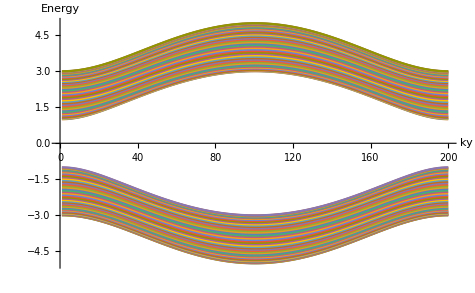

```mathematica
ListLinePlot[Transpose[Table[Sort[Eigenvalues[hx[N[ky],50,3]]],{ky,-Pi,Pi,2*Pi/(200-1)}]],AxesLabel->{HoldForm[ky],HoldForm[Energy]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
{eigs1,vecs1}=Eigensystem[hx[N[-Pi/2],500,1]];
list1=Partition[Riffle[eigs1,vecs1],2];
list2=Sort[list1,#1[[1]]<#2[[1]]&];
```

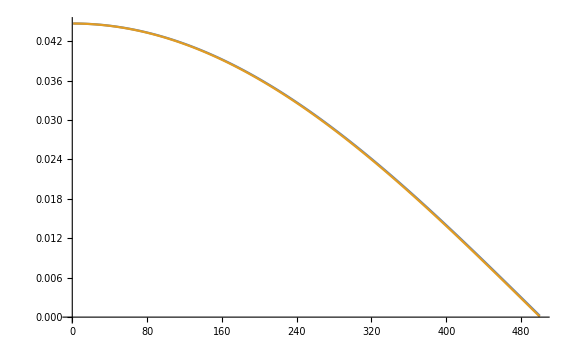

```mathematica
nm=501;
ListLinePlot[{Abs[list2[[nm,2,;;;;2]]],Abs[list2[[nm,2,2;; ;;2]]]},PlotRange->Full]
```

## Assignement 4L part 2

```mathematica
Clear["Global`*"]
Hbhz[kx_,ky_,ϵs_,ϵp_,tss_,tpp_,tsp_,m_]:=Module[{hk},
hk = N[{{ϵs-2*tss*(Cos[kx] + Cos[ky])+m,2tsp*(-ⅈ*Sin[kx]+Sin[ky]),0,0},{2tsp*(ⅈ*Sin[kx]+Sin[ky]),ϵp+2*tpp*(Cos[kx] + Cos[ky])-m,0,0},{0,0,ϵs-2*tss*(Cos[kx] + Cos[ky])-m,2tsp*(-ⅈ*Sin[kx]-Sin[ky])},{0,0,2tsp*(ⅈ*Sin[kx]-Sin[ky]),ϵp+2*tpp*(Cos[kx] + Cos[ky])+m}}]
]
```

```mathematica
Hbhz[kx,ky,ϵs,ϵp,tss,tpp,tsp,m]//MatrixForm
```

(m+ϵs-2. tss (Cos[kx]+Cos[ky]) | 2. tsp ((0.-1. ⅈ) Sin[kx]+Sin[ky]) | 0. | 0.
2. tsp ((0.+1. ⅈ) Sin[kx]+Sin[ky]) | -1. m+ϵp+2. tpp (Cos[kx]+Cos[ky]) | 0. | 0.
0. | 0. | -1. m+ϵs-2. tss (Cos[kx]+Cos[ky]) | 2. tsp ((0.-1. ⅈ) Sin[kx]-1. Sin[ky])
0. | 0. | 2. tsp ((0.+1. ⅈ) Sin[kx]-1. Sin[ky]) | m+ϵp+2. tpp (Cos[kx]+Cos[ky]))

```mathematica
ϵs =-9;
ϵp=-1;
tsp =1;
t = 1.25;
m=4;
Plot3D[Sort[Eigenvalues[Hbhz[kx,ky,ϵs,ϵp,t,t,tsp,m]]],{kx,-Pi,Pi},{ky,-Pi,Pi},AxesLabel->{HoldForm[kx],HoldForm[ky],HoldForm[Energy]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics3D-

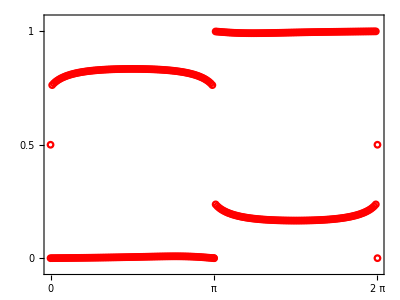
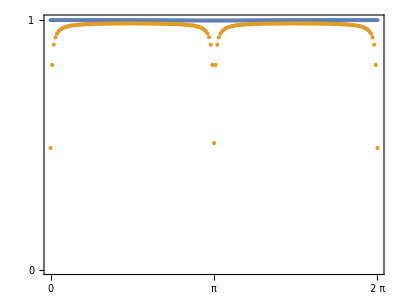

```mathematica
ϵs =-9;
ϵp=-1;
tsp =1;
t = 1.25;
m=4;
Nk=200;
MyMarker=Graphics[{Red,Circle[{0,0},1]}];
kv=Table[N[i],{i,0,2π-2π/Nk,2π/Nk}];
uk=Table[Transpose[Transpose[SortBy[Transpose[Eigensystem[Hbhz[kv[[ki]],kv[[kj]],ϵs,ϵp,t,t,tsp,m]]],First]][[2,1;;2]]],{ki,1,Nk},{kj,1,Nk}];
Pk=Table[uk[[ki,kj]].ConjugateTranspose[uk[[ki,kj]]],{ki,1,Nk},{kj,1,Nk}];
Wilson=Table[ConjugateTranspose[uk[[1,kj]]].(Dot@@Pk[[1;;Nk,kj]]).uk[[1,kj]],{kj,1,Nk}];
WilsonEig = Table[Eigenvalues[Wilson[[kj]]],{kj,1,Nk}];
WilsonEig =Append[WilsonEig ,WilsonEig [[1]]];

{ListPlot[Transpose[Mod[Arg[WilsonEig]/(2π),1]],
PlotStyle->{Blend[{Black,Blue},.5]},PlotMarkers->{MyMarker,.03},
DataRange->{0,2π},PlotRange->{{0,2π},{-0.05,1.05}},AxesOrigin->{0,0.5},
Frame->True,FrameTicks->{{0,π,2π},{0,0.5,1}},
AspectRatio->3/4,ImageSize->400],
ListPlot[Transpose[Abs[WilsonEig]],
DataRange->{0,2π},PlotRange->{{0,2π},{0,1}},
Frame->True,FrameTicks->{{0,π,2π},{0,1}},
AspectRatio->3/4,ImageSize->400]}
```

```mathematica
HObhz[ky_,ϵs_,ϵp_,tss_,tpp_,tsp_,NN_,m_]:=Module[{h0,hp,t0,tp,Tp,T0},
t0=ConstantArray[0,{NN,NN}];
tp=ConstantArray[0,{NN,NN}];
For[i=1,i<=NN,i++,t0[[i,i]]=1;];
For[i=1,i<=NN-1,i++,tp[[i,i+1]]=1;];
h0=N[{{ϵs-2*tss*Cos[ky]+m,2*tsp*Sin[ky],0,0},{2*tsp*Sin[ky],ϵp+2*tpp*Cos[ky]-m,0,0},{0,0,ϵs-2*tss*Cos[ky]-m,-2*tsp*Sin[ky]},{0,0,-2*tsp*Sin[ky],ϵp+2*tpp*Cos[ky]+m}}];
hp=N[{{-tss,tsp,0,0},{-tsp,tpp,0,0},{0,0,-tss,tsp},{0,0,-tsp,tpp}}];
Tp = KroneckerProduct[tp,hp]+ConjugateTranspose[KroneckerProduct[tp,hp]];
T0 =  KroneckerProduct[t0,h0];
T0+Tp
]
```

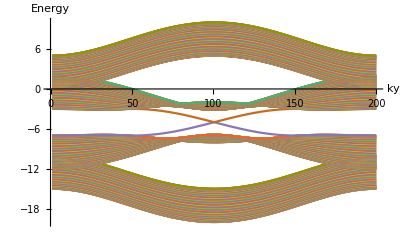

```mathematica
ϵs =-9;
ϵp=-1;
tsp =1;
t = 1.25;
NN=100;
m=6;
ListLinePlot[Transpose[Table[Sort[Eigenvalues[HObhz[ky,ϵs,ϵp,t,t,tsp,NN,m]]],{ky,-Pi,Pi,2*Pi/(200-1)}]],AxesLabel->{HoldForm[ky],HoldForm[Energy]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
ϵs =-9;
ϵp=-1;
tsp =1;
t = 1.25;
A={{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}};
{eigs1,vecs1}=Eigensystem[Hbhz[Pi,Pi,ϵs,ϵp,t,t,tsp]];
list1=Partition[Riffle[eigs1,vecs1],2];
list2=Sort[list1,#1[[1]]<#2[[1]]&];
```

```mathematica
list2//MatrixForm
```

(-6. | {0.,0.,0.,1.}
-6. | {0.,1.,0.,0.}
-4. | {1.,0.,0.,0.}
-4. | {0.,0.,1.,0.})

```mathematica
Hbhz[Pi,Pi,ϵs,ϵp,t,t,tsp]//MatrixForm
A.Conjugate[Hbhz[Pi,Pi,ϵs,ϵp,t,t,tsp]].A
```

(-4. | 4. | 0. | 0.
4. | -6. | 0. | 0.
0. | 0. | -4. | -4.
0. | 0. | -4. | -6.)

{{-4.,-4.,0.,0.},{-4.,-6.,0.,0.},{0.,0.,-4.,4.},{0.,0.,4.,-6.}}

```mathematica
Sort[Eigenvalues[HObhz[Pi,ϵs,ϵp,t,t,tsp,NN]]]
```

{-12.624+0. ⅈ,-12.6214+0. ⅈ,-12.617+0. ⅈ,-12.6108+0. ⅈ,-12.603+0. ⅈ,-12.5933+0. ⅈ,-12.5819+0. ⅈ,-12.5688+0. ⅈ,-12.5539+0. ⅈ,-12.5373+0. ⅈ,-12.5189+0. ⅈ,-12.4987+0. ⅈ,-12.4768+0. ⅈ,-12.4532+0. ⅈ,-12.4277+0. ⅈ,-12.4005+0. ⅈ,-12.3716+0. ⅈ,-12.341+0. ⅈ,-12.3087+0. ⅈ,-12.2738+0. ⅈ,-12.2319+0. ⅈ,-12.1958-0.0292091 ⅈ,-12.1958+0.0292091 ⅈ,-12.1566+0. ⅈ,-12.1054-0.135339 ⅈ,-12.1054+0.135339 ⅈ,-12.088+0. ⅈ,-12.0194-0.240151 ⅈ,-12.0194+0.240151 ⅈ,-12.0108+0. ⅈ,-11.9355-0.342001 ⅈ,-11.9355+0.342001 ⅈ,-11.922+0. ⅈ,-11.8528-0.440846 ⅈ,-11.8528+0.440846 ⅈ,-11.817+0. ⅈ,-11.7708-0.53691 ⅈ,-11.7708+0.53691 ⅈ,-11.6896-0.630143 ⅈ,-11.6896+0.630143 ⅈ,-11.6845+0. ⅈ,-11.6096-0.720265 ⅈ,-11.6096+0.720265 ⅈ,-11.5327-0.8072 ⅈ,-11.5327+0.8072 ⅈ,-11.4966-0.0429158 ⅈ,-11.4966+0.0429158 ⅈ,-11.4641-0.170453 ⅈ,-11.4641+0.170453 ⅈ,-11.4641-0.891983 ⅈ,-11.4641+0.891983 ⅈ,-11.4554-0.287063 ⅈ,-11.4554+0.287063 ⅈ,-11.452-0.863236 ⅈ,-11.452+0.863236 ⅈ,-11.452-0.387857 ⅈ,-11.452+0.387857 ⅈ,-11.4516-0.758695 ⅈ,-11.4516+0.758695 ⅈ,-11.4515-0.69776 ⅈ,-11.4515+0.69776 ⅈ,-11.4513-0.631291 ⅈ,-11.4513+0.631291 ⅈ,-11.4512-0.814145 ⅈ,-11.4512+0.814145 ⅈ,-11.4509-0.477669 ⅈ,-11.4509+0.477669 ⅈ,-11.4509-0.558284 ⅈ,-11.4509+0.558284 ⅈ,-11.4462-0.916333 ⅈ,-11.4462+0.916333 ⅈ,-11.4398-0.950107 ⅈ,-11.4398+0.950107 ⅈ,-11.4357-0.978531 ⅈ,-11.4357+0.978531 ⅈ,-11.4309-1.00409 ⅈ,-11.4309+1.00409 ⅈ,-11.4264-1.02826 ⅈ,-11.4264+1.02826 ⅈ,-11.4226-1.05055 ⅈ,-11.4226+1.05055 ⅈ,-11.4194-1.07066 ⅈ,-11.4194+1.07066 ⅈ,-11.4166-1.08868 ⅈ,-11.4166+1.08868 ⅈ,-11.4142-1.10462 ⅈ,-11.4142+1.10462 ⅈ,-11.4122-1.11847 ⅈ,-11.4122+1.11847 ⅈ,-11.4105-1.13021 ⅈ,-11.4105+1.13021 ⅈ,-11.4092-1.13983 ⅈ,-11.4092+1.13983 ⅈ,-11.4082-1.14729 ⅈ,-11.4082+1.14729 ⅈ,-11.4074-1.15267 ⅈ,-11.4074+1.15267 ⅈ,-11.4071-1.15585 ⅈ,-11.4071+1.15585 ⅈ,-11.+0. ⅈ,-10.6563+0. ⅈ,-10.6548+0. ⅈ,-10.6522+0. ⅈ,-10.6486+0. ⅈ,-10.644+0. ⅈ,-10.6384+0. ⅈ,-10.6317+0. ⅈ,-10.6241+0. ⅈ,-10.6155+0. ⅈ,-10.6059+0. ⅈ,-10.5953+0. ⅈ,-10.5838+0. ⅈ,-10.5714+0. ⅈ,-10.5581+0. ⅈ,-10.5439+0. ⅈ,-10.5289+0. ⅈ,-10.513+0. ⅈ,-10.4963+0. ⅈ,-10.4788+0. ⅈ,-10.4606+0. ⅈ,-10.4416+0. ⅈ,-10.4219+0. ⅈ,-10.4015+0. ⅈ,-10.3805+0. ⅈ,-10.3589+0. ⅈ,-10.3366+0. ⅈ,-10.3139+0. ⅈ,-10.2906+0. ⅈ,-10.2669+0. ⅈ,-10.2427+0. ⅈ,-10.2181+0. ⅈ,-10.1932+0. ⅈ,-10.1679+0. ⅈ,-10.1423+0. ⅈ,-10.1165+0. ⅈ,-10.0904+0. ⅈ,-10.0642+0. ⅈ,-10.0378+0. ⅈ,-10.0114+0. ⅈ,-9.98483+0. ⅈ,-9.95828+0. ⅈ,-9.93174+0. ⅈ,-9.90525+0. ⅈ,-9.87885+0. ⅈ,-9.85257+0. ⅈ,-9.82645+0. ⅈ,-9.80053+0. ⅈ,-9.77483+0. ⅈ,-9.74939+0. ⅈ,-9.72425+0. ⅈ,-9.69943+0. ⅈ,-9.67495+0. ⅈ,-9.65086+0. ⅈ,-9.62718+0. ⅈ,-9.60393+0. ⅈ,-9.58114+0. ⅈ,-9.55882+0. ⅈ,-9.537+0. ⅈ,-9.5157+0. ⅈ,-9.49494+0. ⅈ,-9.47473+0. ⅈ,-9.45508+0. ⅈ,-9.43601+0. ⅈ,-9.41753+0. ⅈ,-9.39965+0. ⅈ,-9.38236+0. ⅈ,-9.36569+0. ⅈ,-9.34963+0. ⅈ,-9.33418+0. ⅈ,-9.31935+0. ⅈ,-9.30513+0. ⅈ,-9.29152+0. ⅈ,-9.27852+0. ⅈ,-9.26612+0. ⅈ,-9.25432+0. ⅈ,-9.2431+0. ⅈ,-9.23247+0. ⅈ,-9.2224+0. ⅈ,-9.2129+0. ⅈ,-9.20394+0. ⅈ,-9.19553+0. ⅈ,-9.18764+0. ⅈ,-9.18027+0. ⅈ,-9.1734+0. ⅈ,-9.16702+0. ⅈ,-9.16112+0. ⅈ,-9.15569+0. ⅈ,-9.15071+0. ⅈ,-9.14618+0. ⅈ,-9.14208+0. ⅈ,-9.13841+0. ⅈ,-9.13515+0. ⅈ,-9.13229+0. ⅈ,-9.12983+0. ⅈ,-9.12776+0. ⅈ,-9.12608+0. ⅈ,-9.12478+0. ⅈ,-9.12385+0. ⅈ,-9.12329+0. ⅈ,-9.+0. ⅈ,-7.+0. ⅈ,-6.59295-1.15586 ⅈ,-6.59295+1.15586 ⅈ,-6.59253-1.15265 ⅈ,-6.59253+1.15265 ⅈ,-6.59181-1.14731 ⅈ,-6.59181+1.14731 ⅈ,-6.5908-1.13981 ⅈ,-6.5908+1.13981 ⅈ,-6.58946-1.1302 ⅈ,-6.58946+1.1302 ⅈ,-6.58782-1.11849 ⅈ,-6.58782+1.11849 ⅈ,-6.58576-1.10461 ⅈ,-6.58576+1.10461 ⅈ,-6.58339-1.0887 ⅈ,-6.58339+1.0887 ⅈ,-6.58058-1.07062 ⅈ,-6.58058+1.07062 ⅈ,-6.57732-1.0505 ⅈ,-6.57732+1.0505 ⅈ,-6.57351-1.02838 ⅈ,-6.57351+1.02838 ⅈ,-6.5693-1.00427 ⅈ,-6.5693+1.00427 ⅈ,-6.5646-0.977885 ⅈ,-6.5646+0.977885 ⅈ,-6.55874-0.949514 ⅈ,-6.55874+0.949514 ⅈ,-6.55583-0.0819555 ⅈ,-6.55583+0.0819555 ⅈ,-6.55232-0.920305 ⅈ,-6.55232+0.920305 ⅈ,-6.54714-0.888302 ⅈ,-6.54714+0.888302 ⅈ,-6.5419-0.246035 ⅈ,-6.5419+0.246035 ⅈ,-6.53944-0.850907 ⅈ,-6.53944+0.850907 ⅈ,-6.52718-0.790686 ⅈ,-6.52718+0.790686 ⅈ,-6.52652-0.738268 ⅈ,-6.52652+0.738268 ⅈ,-6.52251-0.408621 ⅈ,-6.52251+0.408621 ⅈ,-6.521-0.681164 ⅈ,-6.521+0.681164 ⅈ,-6.5206-0.819835 ⅈ,-6.5206+0.819835 ⅈ,-6.51594-0.615426 ⅈ,-6.51594+0.615426 ⅈ,-6.51589-0.554787 ⅈ,-6.51589+0.554787 ⅈ,-6.49768-0.48236 ⅈ,-6.49768+0.48236 ⅈ,-6.47089-0.349037 ⅈ,-6.47089+0.349037 ⅈ,-6.44124-0.721004 ⅈ,-6.44124+0.721004 ⅈ,-6.42885-0.200723 ⅈ,-6.42885+0.200723 ⅈ,-6.38758+0. ⅈ,-6.34531-0.629355 ⅈ,-6.34531+0.629355 ⅈ,-6.24291-0.542536 ⅈ,-6.24291+0.542536 ⅈ,-6.13924-0.460573 ⅈ,-6.13924+0.460573 ⅈ,-6.06865+0. ⅈ,-6.03698-0.382975 ⅈ,-6.03698+0.382975 ⅈ,-5.95153+0. ⅈ,-5.93666-0.309321 ⅈ,-5.93666+0.309321 ⅈ,-5.84623+0. ⅈ,-5.83805-0.240123 ⅈ,-5.83805+0.240123 ⅈ,-5.75178+0. ⅈ,-5.7419-0.177262 ⅈ,-5.7419+0.177262 ⅈ,-5.67025+0. ⅈ,-5.65063-0.122889 ⅈ,-5.65063+0.122889 ⅈ,-5.60015+0. ⅈ,-5.56747-0.0785727 ⅈ,-5.56747+0.0785727 ⅈ,-5.54013+0. ⅈ,-5.49597-0.045376 ⅈ,-5.49597+0.045376 ⅈ,-5.4889+0. ⅈ,-5.44783+0. ⅈ,-5.4389-0.0232383 ⅈ,-5.4389+0.0232383 ⅈ,-5.41577+0. ⅈ,-5.39881-0.0105388 ⅈ,-5.39881+0.0105388 ⅈ,-5.39177+0. ⅈ,-5.37992+0. ⅈ,-5.37715-0.00267929 ⅈ,-5.37715+0.00267929 ⅈ,-1.+0. ⅈ,-0.876709+0. ⅈ,-0.876153+0. ⅈ,-0.875224+0. ⅈ,-0.87392+0. ⅈ,-0.872236+0. ⅈ,-0.870168+0. ⅈ,-0.867709+0. ⅈ,-0.864853+0. ⅈ,-0.861592+0. ⅈ,-0.857917+0. ⅈ,-0.853819+0. ⅈ,-0.849287+0. ⅈ,-0.84431+0. ⅈ,-0.838878+0. ⅈ,-0.832979+0. ⅈ,-0.826601+0. ⅈ,-0.819732+0. ⅈ,-0.81236+0. ⅈ,-0.804472+0. ⅈ,-0.796057+0. ⅈ,-0.787103+0. ⅈ,-0.777599+0. ⅈ,-0.767535+0. ⅈ,-0.756899+0. ⅈ,-0.745684+0. ⅈ,-0.733881+0. ⅈ,-0.721482+0. ⅈ,-0.708481+0. ⅈ,-0.694872+0. ⅈ,-0.680653+0. ⅈ,-0.66582+0. ⅈ,-0.650373+0. ⅈ,-0.634311+0. ⅈ,-0.617637+0. ⅈ,-0.600355+0. ⅈ,-0.582469+0. ⅈ,-0.563987+0. ⅈ,-0.544918+0. ⅈ,-0.525271+0. ⅈ,-0.505059+0. ⅈ,-0.484296+0. ⅈ,-0.462997+0. ⅈ,-0.44118+0. ⅈ,-0.418864+0. ⅈ,-0.396069+0. ⅈ,-0.372819+0. ⅈ,-0.349136+0. ⅈ,-0.325045+0. ⅈ,-0.300575+0. ⅈ,-0.275752+0. ⅈ,-0.250607+0. ⅈ,-0.22517+0. ⅈ,-0.199473+0. ⅈ,-0.173548+0. ⅈ,-0.147429+0. ⅈ,-0.121152+0. ⅈ,-0.0947512+0. ⅈ,-0.0682632+0. ⅈ,-0.0417246+0. ⅈ,-0.0151729+0. ⅈ,0.0113545+0. ⅈ,0.0378194+0. ⅈ,0.0641836+0. ⅈ,0.0904088+0. ⅈ,0.116456+0. ⅈ,0.142288+0. ⅈ,0.167866+0. ⅈ,0.193151+0. ⅈ,0.218107+0. ⅈ,0.242695+0. ⅈ,0.266879+0. ⅈ,0.290622+0. ⅈ,0.313888+0. ⅈ,0.336643+0. ⅈ,0.358851+0. ⅈ,0.38048+0. ⅈ,0.401495+0. ⅈ,0.421866+0. ⅈ,0.441561+0. ⅈ,0.460551+0. ⅈ,0.478806+0. ⅈ,0.496298+0. ⅈ,0.513002+0. ⅈ,0.528892+0. ⅈ,0.543943+0. ⅈ,0.558133+0. ⅈ,0.57144+0. ⅈ,0.583844+0. ⅈ,0.595327+0. ⅈ,0.60587+0. ⅈ,0.615457+0. ⅈ,0.624075+0. ⅈ,0.63171+0. ⅈ,0.638351+0. ⅈ,0.643987+0. ⅈ,0.64861+0. ⅈ,0.652213+0. ⅈ,0.65479+0. ⅈ,0.656338+0. ⅈ}